```mathematica
196+FromDigits[Sort[IntegerDigits[196]]]
```

```mathematica
sta[i_Integer,m_Integer,v_Integer]:=ArrayPlot[PadLeft[IntegerDigits[NestWhileList[(#+FromDigits[Sort[IntegerDigits[#]]])&,i,FromDigits[Sort[IntegerDigits[#]]]=!=# &,1,m],v]]]
```

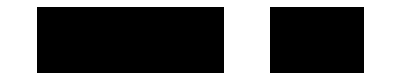

```mathematica
sta[123, 500, 2]
```

```mathematica
IntegerDigits[16,2]
```

{1,0,0,0,0}